## GME Lukin-Structure

NOTE: Some calculations are made using ParallelDo or ParallelTable, that use several cores of the CPU.

### Parameters

```mathematica
T0=AbsoluteTime[];
SetDirectory[NotebookDirectory[]];
(**************************************************)
(*parameters of the structure*)
a=1.0;(*lattice parameter*)
we=0.01;(*parameter used in the searching of the guided modes*)
rs=0.0833 ; (*radio of the outer holes *)
rl=0.15; (*radio of the inner holes*)
l=0.4; (* distance of the inner holes to the center of the unit cell*)
d=0.25 ; (*slab width*)
ex1=1; (*permittivity of the upper layer*)
ex3=1; (*permittivity of the lower layer*)
es=10.5625; (*permittivity of the slab backfground*)
er=1.0; (*permi+ttivity of the holes in the slab*)
S=Sqrt[3]/2*a^2; (*area of the unit cell*)
(*parameters of the calculation*)
gx=gy=9;(*Must be integer, give a idea of the basis size of the in-plane reciprocal lattice vector*)
Ng=3;(*Must be integer, number of guided modes for each g*)
sig=1;(*Must be integer*)
(**************************************************)
```

```mathematica
Clear[coef,coef1, coef2,G,Cet,epsm,NTE,A2,B2,A3,NTM,C2,D2,C3,W1,W2,W3,X1,X2,X3,Y1,Y2,Y3,Z1,Z2,Z3];
```

```mathematica
Norm[{1/√3,1}]
```

2/(√3)

#### Basis of PW, circular cutoff

Here, the program select the set of G that will use to build up the basis of guided modes. It use a circular cutoff to chose the set, it is all the G vectos that satisfie the condition G ≤Gmax= gx* (4π)/(√3 a)

```mathematica
gg[n_,m_]:=2 π/a N[n*{1/√3,1}+m*{-1/√3,1}];gr[n_,m_,θ_]:=2π/a {{Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}}.(n*{1/√3,1}+m*{-1/√3,1});Gmax=Norm[gg[gx,0]];
Gg={};
Do[ Do[If[Norm[gg[i,j]]≤Gmax,AppendTo[Gg,{i,j}]],{i,-2gx,2gx}],{j,-2gy,2gy}];
G[m_]:=G[m]=N[gg[Gg⟦m,1⟧,Gg⟦m,2⟧]];
lg=Length[Gg];
gmax=Max[Gg⟦All,1⟧];
Print["The set of G vectors have ", lg, " elements"]
```

The set of G vectors have 301 elements

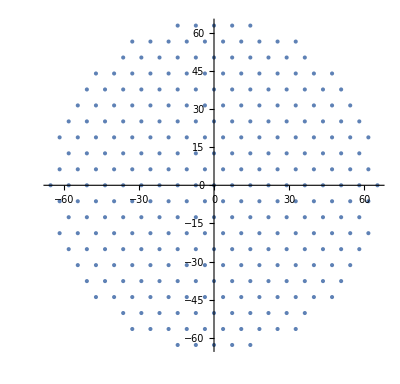

```mathematica
ListPlot[Table[G[m],{m,lg}],AspectRatio->Automatic] 
(*Each point in the plot represent a G vector we will use to build up the guided modes*)
```

### Permitivity Structure

Here, we define functions to describe the structure of the dielectric media. First, we define a piecewise function with the exact value of the permittivity at any r in the unit cell. Second, we  calculate the Fourier coefficients to expand the dielectric permittivity in the plane and construct the matrix elements η_(G-G')associated with the structure of the unit cell.

#### Analytic Dielectric Function

```mathematica
(*Mesh in the hexagonal unit cell to evaluated the permittivity, fields, Green functions or any other function of the position*)
Rlist=Flatten[Table[N[{xx,yy}],{xx,-Sqrt[3]/3,Sqrt[3]/3,(2/3Sqrt[3]/3)/50},{yy,-0.5,0.5,1/50}],1]; (*Mesh in a rectangular area*)
RHex={};(*Mesh in a hexagonal (unit cell) area*)
Do[{xX,yY}=Rlist⟦i⟧;
If[(Abs[xX]≤ Sqrt[3]/6 && Abs[yY] <=0.5),AppendTo[RHex,{xX,yY}],If[Abs[xX]≥  Sqrt[3]/6&& Abs[yY]≤  -Sqrt[3]Abs[xX]+1,AppendTo[RHex,{xX,yY}]]],{i,1,Length[Rlist]}];
(*Below, we define the analytical piecewise dielectric function in the unit cell*)
Eps[x_,y_]:=es-If[(Norm[Abs[{x,y}]-{Sqrt[3]/3,0}]≤ rs||Norm[Abs[{x,y}]-{Sqrt[3]/6,0.5}]≤ rs||Norm[Abs[{x,y}]-{0,0.5}]≤ rl||Norm[Abs[{x,y}]-{Sqrt[3]/4,0.25}]≤ rl),es-er,0]
```

```mathematica
EpsList=Table[{RHex⟦i,1⟧,RHex⟦i,2⟧,Eps[RHex⟦i,1⟧,RHex⟦i,2⟧]},{i,1,Length[RHex]}]; (*Evaluating the dielectric function in the unit cell mesh*)
```

```mathematica
(*We define the plot of the dielectric function, to be used before in some graphs*)
EpsGrap=ListDensityPlot[EpsList,ColorFunction->"GrayTones",PlotStyle-> Opacity[0.1]];
EpsGrapFull=ListDensityPlot[EpsList,ColorFunction->"GrayTones"];
```

#### Coefficients of dielectric structure

```mathematica
(*Here we construct the Fourier coefficients of the dielectric function*)
II[Gx_,Gy_]:=II[Gx,Gy]=NIntegrate[Integrate[Exp[ⅈ {Gx,Gy}.{xx,yy}],{xx,-√(rl^2-(0.5 a-l+yy)^2),0}],{yy,-(0.5 a-l+rl),0}]+NIntegrate[Integrate[Exp[ⅈ {Gx,Gy}.{xx,yy}],{xx,-√(rl^2-(0.5 a-l-yy)^2),0}],{yy,0,(0.5 a-l+rl)}]+NIntegrate[Integrate[Exp[ⅈ {Gx,Gy}.{xx,yy}],{xx,0,√(rl^2-(0.5 a-l+yy)^2)}],{yy,-(0.5 a-l+rl),0}]+NIntegrate[Integrate[Exp[ⅈ {Gx,Gy}.{xx,yy}],{xx,0,√(rl^2-(0.5 a-l-yy)^2)}],{yy,0,(0.5 a-l+rl)}];
coef1[n_,m_]:=coef1[n,m]=(er-es)/(√3 a^2/2)*If[Norm[gg[n,m]]==0, 2π rs^2,2 π rs BesselJ[1, rs Norm[gg[n,m]]]/Norm[gg[n,m]](Exp[ⅈ gg[n,m].{√3 a/3,0}]+Exp[ⅈ gg[n,m].{-√3 a/3,0}])];
coef2[n_,m_]:=coef2[n,m]=(er-es)/(√3 a^2/2)(Exp[ⅈ gg[n,m].{0,-0.5*a}]*II[gg[n,m][[1]],gg[n,m][[2]]]+Exp[ⅈ gg[n,m].{-√3 a/4,a/4}]II[gr[n,m,π/3][[1]],gr[n,m,π/3][[2]]]+Exp[ⅈ gg[n,m].{√3 a/4,a/4}]II[gr[n,m,-π/3][[1]],gr[n,m,-π/3][[2]]]);
coef[n_,m_]:=coef[n,m]=coef[-n,-m]=coef[m,n]=If[Norm[gg[n,m]]==0, es+coef1[n,m]+coef2[n,m],coef1[n,m]+coef2[n,m]];
```

```mathematica
Tcoef0=AbsoluteTime[];
Coef=ConstantArray[0,{4*gmax+1,4*gmax+1}];
 Do[Coef[[2gmax+1+n,2gmax+1+n;;4gmax+1]]=ParallelTable[Chop[coef[n,m]],{m,n,2gmax}];
Coef[[2gmax+1+n;;4gmax+1,2gmax+1+n]]=Coef[[2gmax+1+n,2gmax+1+n;;4gmax+1]],{n,-2gmax,2gmax}];
Tcoef=AbsoluteTime[]-Tcoef0;
Print["Spent time in evaluate the Fourier coefficients: ", IntegerPart[Tcoef/3600],"hrs, ",IntegerPart[Mod[Tcoef,3600]/60],"mins, ",Mod[Tcoef,60],"s."]
```

Spent time in evaluate the Fourier coefficients: 0hrs, 3mins, 33.353973s.

```mathematica
(*We export the coefficients to be used in other programs, because it could take a long time dependinmg on the G elements*)
Export["Coef-Eps-gmax_"<>ToString[gx]<>"-Ng_"<>ToString[Ng]<>".dat",Coef,"Table"];
```

```mathematica
Coef=Import["Coef-Eps-gmax_"<>ToString[gx]<>"-Ng_"<>ToString[Ng]<>".dat"];
```

#### Matrix for permitivity coeffients

```mathematica
(*In this part, the matriz Subscript[η, g-G'] (Cet), is calculated for the three spacial regions l=1(air),2 (PC slab),3 (air)*)
Clear[Mes];TMes=AbsoluteTime[];Mes=ParallelTable[Coef⟦2gmax+1+Gg⟦m,1⟧-Gg⟦mp,1⟧,2gmax+1 +Gg⟦m,2⟧-Gg⟦mp,2⟧⟧,{m,Length[Gg]},{mp,Length[Gg]}];
Mets=Inverse[Mes];
Cet[l_,m_,mp_]:=Cet[l,m,mp]=N[If[l==1,N[(1/ex1)]*IdentityMatrix[Length[Gg]][[m,mp]],If[l==2,Mets[[m,mp]],If[l==3,N[(1/ex3)]*IdentityMatrix[Length[Gg]][[m,mp]]]]]];
epsm[j_]:=epsm[j]=N[(2/(a a Sqrt[3])) If[j==1,ex1 a a Sqrt[3]/2,If[j==2,es*(a a Sqrt[3]/2-3*II[0,0]-2 π rs^2)+(3*II[0,0]+2 π rs^2)er,ex3 a a Sqrt[3]/2]]];
TMes=AbsoluteTime[]-TMes;
Print["Spent time in Mes: ", IntegerPart[TMes/3600],"hrs, ",IntegerPart[Mod[TMes,3600]/60],"mins, ",Mod[TMes,60],"s."]
```

Spent time in Mes: 0hrs, 0mins, 0.225577s.

```mathematica
(*Here, we use the matrix Mets to evaluate the coefficcients of the inverse of dielectric function*)Coefinv=Table[Mets⟦(Length[Mets]+1)/2,i⟧,{i,Length[Mets]}];
```

```mathematica
(*Again, we export the Mets matrix to save time in the follow notebooks*)
Export["Matrix-Eta-gmax_"<>ToString[gx]<>"-Ng_"<>ToString[Ng]<>".dat",Mets,"Table"];
```

```mathematica
Mets=Import["Matrix-Eta-gmax_"<>ToString[gx]<>"-Ng_"<>ToString[Ng]<>".dat","Table"];
```

#### Plotting the expansion of permittivity

```mathematica
epsop[x_,y_]:=Chop[Sum[Coef[[2*gmax+1+Gg[[i,1]],2gmax +1+Gg[[i,2]] ]] Exp[N[I G[i].{x,y}]],{i,Length[Gg]}]];
eps3D[x_,y_,z_]:=If[Abs[z]<=0.5d,epsop[x,y],1];
epsinvop[x_,y_]:=Chop[Sum[Coefinv[[i]] Exp[N[I G[i].{x,y}]],{i,Length[Gg]}]];
```

```mathematica
listaepsop=ParallelTable[{x,y,epsop[x,y]},{x,-2Sqrt[3]/3,2Sqrt[3]/3,0.01},{y,-0.5,0.5,0.01}];
```

```mathematica
listaepsinvop=Table[{x,y,epsinvop[x,y]},{x,-2Sqrt[3]/3,2Sqrt[3]/3,0.01},{y,-0.5,0.5,0.01}];
```

```mathematica
ListDensityPlot[Flatten[listaepsinvop,1],AspectRatio->Automatic, PlotLegends-> Automatic]
(*ListDensityPlot[Flatten[listaEpsInvop,1],AspectRatio->Automatic, PlotLegends-> Automatic]*)
```

-Graphics-

```mathematica
Show[{ListDensityPlot[Flatten[listaepsop,1],ColorFunction->"TemperatureMap",FrameTicksStyle->Directive[Black,20],PlotRange->All,ColorFunction->"TemperatureMap",PlotLegends->Automatic,AspectRatio->Automatic],ListPlot[{{{-2Sqrt[3]/3,0},{2Sqrt[3]/3,0}},{{0,0}},{{0,-0.5},{0,0.5}}},Joined->True]}]
```

-Graphics-

### Init Structure

Here, we define some function to calculate the guided modes

```mathematica
X[j_,g_,w_]:=N[Sqrt[g^2-epsm[j] (w^2)]];
qg[g_,w_]:=N[Sqrt[epsm[2] (w^2)-g^2]];
TEsigp[g_,w_]:=N[qg[g,w] Sin[qg[g,w] 0.5 d]-X[1,g,w] Cos[qg[g,w] 0.5 d]];
TEsigm[g_,w_]:=N[qg[g,w] Cos[qg[g,w] 0.5 d]+X[1,g,w] Sin[qg[g,w] 0.5 d]];
TMsigp[g_,w_]:=N[(qg[g,w]/epsm[2]) Cos[qg[g,w] 0.5 d]+(X[1,g,w]/epsm[1]) Sin[qg[g,w] 0.5 d]];
TMsigm[g_,w_]:=N[(qg[g,w]/epsm[2]) Sin[qg[g,w] 0.5 d]-(X[1,g,w]/epsm[1]) Cos[qg[g,w] 0.5 d]];
If[sig==1,If[Mod[Ng,2]==0,Ngte=Ngtm=Ng/2,Ngte=0.5 (Ng+1);
Ngtm=0.5 (Ng-1)],If[Mod[Ng,2]==0,Ngte=Ngtm=Ng/2,Ngte=0.5 (Ng-1);
Ngtm=0.5 (Ng+1)]];
eg[g_]:=Normalize[{-g[[2]],g[[1]]}];
A2p[g_,w_]:=N[0.5 (qg[g,w]-I X[1,g,w]) Exp[I qg[g,w] 0.5 d]/qg[g,w]];
B2p[g_,w_]:=N[0.5 (qg[g,w]+I X[1,g,w]) Exp[-I qg[g,w] 0.5 d]/qg[g,w]];
A3p[g_,w_]:=N[0.5 (qg[g,w] (X[3,g,w]-X[1,g,w]) Cos[qg[g,w] d]+(qg[g,w]^2+X[1,g,w] X[3,g,w]) Sin[qg[g,w] d])/(qg[g,w] X[3,g,w])];
NTE[g_,w_]:=NTE[g,w]=Chop[Sqrt[1/(((X[1,g,w]^2+g^2)/(2 X[1,g,w]))+(((X[3,g,w]^2+g^2) (Norm[A3p[g,w]]^2))/(2 X[3,g,w]))+d ((g^2+qg[g,w]^2) (Norm[A2p[g,w]]^2+Norm[B2p[g,w]]^2)+((g^2-qg[g,w]^2) (Conjugate[A2p[g,w]] B2p[g,w]+Conjugate[B2p[g,w]] A2p[g,w]) Sin[qg[g,w] d]/(qg[g,w] d))))]];
A2[g_,w_]:=A2[g,w]=NTE[g,w] A2p[g,w];
B2[g_,w_]:=B2[g,w]=NTE[g,w] B2p[g,w];
A3[g_,w_]:=A3[g,w]=NTE[g,w] A3p[g,w];
C2p[g_,w_]:=((qg[g,w]/epsm[2])-I (X[1,g,w]/epsm[1])) Exp[I qg[g,w] d/2]/(2 (qg[g,w]/epsm[2]));
D2p[g_,w_]:=((qg[g,w]/epsm[2])+I (X[1,g,w]/epsm[1])) Exp[-I qg[g,w] d/2]/(2 (qg[g,w]/epsm[2]));
C3p[g_,w_]:=((qg[g,w]/epsm[2]) ((X[3,g,w]/epsm[3])-(X[1,g,w]/epsm[1])) Cos[qg[g,w] d]+((qg[g,w]/epsm[2])^2+(X[1,g,w]/epsm[1]) (X[3,g,w]/epsm[3])) Sin[qg[g,w] d])/(2 (qg[g,w]/epsm[2]) (X[3,g,w]/epsm[3]));
NTM[g_,w_]:=NTM[g,w]=Chop[Sqrt[1/((1/(2 X[1,g,w]))+((Norm[C3p[g,w]]^2)/(2 X[3,g,w]))+d (Norm[C2p[g,w]]^2+Norm[D2p[g,w]]^2+(Conjugate[C2p[g,w]] D2p[g,w]+Conjugate[D2p[g,w]] C2p[g,w]) Sin[qg[g,w] d]/(qg[g,w] d)))]];
C2[g_,w_]:=C2[g,w]=NTM[g,w] C2p[g,w];
D2[g_,w_]:=D2[g,w]=NTM[g,w] D2p[g,w];
C3[g_,w_]:=C3[g,w]=NTM[g,w] C3p[g,w];
I1[g_,gp_,w_,wp_]:=(X[1,g,w]+X[1,gp,wp])^(-1);
I2p[g_,gp_,w_,wp_]:=Sin[(qg[g,w]+qg[gp,wp]) d/2]/((qg[g,w]+qg[gp,wp])/2);
I2m[g_,gp_,w_,wp_]:=If[(qg[g,w]-qg[gp,wp])==0,d,Sin[(qg[g,w]-qg[gp,wp]) d/2]/((qg[g,w]-qg[gp,wp])/2)];
I3[g_,gp_,w_,wp_]:=(X[3,g,w]+X[3,gp,wp])^(-1);
q[j_,g_,w_]:=N[Sqrt[epsm[j] (w^2)-g^2]];
Mte21[g_,w_]:=N[(1/(2 q[2,g,w]))*{{(q[2,g,w]+q[1,g,w]) Exp[0.5I q[2,g,w] d],(q[2,g,w]-q[1,g,w]) Exp[0.5I q[2,g,w] d]},{(q[2,g,w]-q[1,g,w]) Exp[-0.5I q[2,g,w] d],(q[2,g,w]+q[1,g,w]) Exp[-0.5I q[2,g,w] d]}}];
Mte32[g_,w_]:=N[(0.5/ q[3,g,w])*{{(q[3,g,w]+q[2,g,w]) Exp[0.5I q[2,g,w] d],(q[3,g,w]-q[2,g,w]) Exp[-0.5I q[2,g,w] d]},{(q[3,g,w]-q[2,g,w]) Exp[0.5I q[2,g,w] d],(q[3,g,w]+q[2,g,w]) Exp[-0.5I q[2,g,w] d]}}];
Mte31[g_,w_]:=N[(0.25/(q[2,g,w]q[3,g,w])){{(q[2,g,w]+q[1,g,w])(q[3,g,w]+q[2,g,w])Exp[I q[2,g,w] d]+(q[2,g,w]-q[1,g,w])(q[3,g,w]-q[2,g,w])Exp[-I q[2,g,w] d],(q[2,g,w]-q[1,g,w])(q[3,g,w]+q[2,g,w])Exp[I q[2,g,w] d]+(q[2,g,w]+q[1,g,w])(q[3,g,w]-q[2,g,w])Exp[-I q[2,g,w] d]},{(q[2,g,w]+q[1,g,w])(q[3,g,w]-q[2,g,w])Exp[I q[2,g,w] d]+(q[2,g,w]-q[1,g,w])(q[3,g,w]+q[2,g,w])Exp[-I q[2,g,w] d],(q[2,g,w]-q[1,g,w])(q[3,g,w]-q[2,g,w])Exp[I q[2,g,w] d]+(q[2,g,w]+q[1,g,w])(q[3,g,w]+q[2,g,w])Exp[-I q[2,g,w] d]}}];
X1l=N[1/Sqrt[epsm[1]]];
W1l[g_,w_]:=-(Mte31[g,w][[1,2]]/Mte31[g,w][[1,1]]) X1l;
W2l[g_,w_]:=Mte21[g,w][[1,1]] W1l[g,w]+Mte21[g,w][[1,2]] X1l;
X2l[g_,w_]:=Mte21[g,w][[2,1]] W1l[g,w]+Mte21[g,w][[2,2]] X1l;
W3l=N[0];
X3l[g_,w_]:=Mte32[g,w][[2,1]] W2l[g,w]+Mte32[g,w][[2,2]] X2l[g,w];
W3u=N[1/Sqrt[epsm[3]]];
X3u[g_,w_]:=(Mte31[g,w][[2,1]]/Mte31[g,w][[1,1]]) W3u;
W1u[g_,w_]:=W3u/Mte31[g,w][[1,1]];
X1u=N[0];
W2u[g_,w_]:=Mte21[g,w][[1,1]] W1u[g,w];
X2u[g_,w_]:=Mte21[g,w][[2,1]] W1u[g,w];
W1[g_,w_,j_]:=W1[g,w,j]=If[j==1,W1l[g,w],If[j==3,W1u[g,w]]];
W2[g_,w_,j_]:=W2[g,w,j]=If[j==1,W2l[g,w],If[j==3,W2u[g,w]]];
W3[g_,w_,j_]:=W3[g,w,j]=If[j==1,W3l,If[j==3,W3u]];
X1[g_,w_,j_]:=X1[g,w,j]=If[j==1,X1l,If[j==3,X1u]];
X2[g_,w_,j_]:=X2[g,w,j]=If[j==1,X2l[g,w],If[j==3,X2u[g,w]]];
X3[g_,w_,j_]:=X3[g,w,j]=If[j==1,X3l[g,w],If[j==3,X3u[g,w]]];
Mtm21[g_,w_]:=N[(0.5/(q[2,g,w]/epsm[2]))*{{((q[2,g,w]/epsm[2])+(q[1,g,w]/epsm[1])) Exp[0.5I q[2,g,w] d],((q[2,g,w]/epsm[2])-(q[1,g,w]/epsm[1])) Exp[0.5I q[2,g,w] d]},{((q[2,g,w]/epsm[2])-(q[1,g,w]/epsm[1])) Exp[-0.5I q[2,g,w] d],((q[2,g,w]/epsm[2])+(q[1,g,w]/epsm[1])) Exp[-0.5I q[2,g,w] d]}}];
Mtm32[g_,w_]:=N[(0.5/(q[3,g,w]/epsm[3]))*{{((q[3,g,w]/epsm[3])+(q[2,g,w]/epsm[2])) Exp[0.5I q[2,g,w] d],((q[3,g,w]/epsm[3])-(q[2,g,w]/epsm[2])) Exp[-0.5I q[2,g,w] d]},{((q[3,g,w]/epsm[3])-(q[2,g,w]/epsm[2])) Exp[0.5I q[2,g,w] d],((q[3,g,w]/epsm[3])+(q[2,g,w]/epsm[2])) Exp[-0.5I q[2,g,w] d]}}];
Mtm31[g_,w_]:=N[(0.25/(q[2,g,w]q[3,g,w]/(epsm[2]epsm[3]))){{(q[2,g,w]/epsm[2]+q[1,g,w]/epsm[1])(q[3,g,w]/epsm[3]+q[2,g,w]/epsm[2])Exp[I q[2,g,w] d]+(q[2,g,w]/epsm[2]-q[1,g,w]/epsm[1])(q[3,g,w]/epsm[3]-q[2,g,w]/epsm[2])Exp[-I q[2,g,w] d],(q[2,g,w]/epsm[2]-q[1,g,w]/epsm[1])(q[3,g,w]/epsm[3]+q[2,g,w]/epsm[2])Exp[I q[2,g,w] d]+(q[2,g,w]/epsm[2]+q[1,g,w]/epsm[1])(q[3,g,w]/epsm[3]-q[2,g,w]/epsm[2])Exp[-I q[2,g,w] d]},{(q[2,g,w]/epsm[2]+q[1,g,w]/epsm[1])(q[3,g,w]/epsm[3]-q[2,g,w]/epsm[2])Exp[I q[2,g,w] d]+(q[2,g,w]/epsm[2]-q[1,g,w]/epsm[1])(q[3,g,w]/epsm[3]+q[2,g,w]/epsm[2])Exp[-I q[2,g,w] d],(q[2,g,w]/epsm[2]-q[1,g,w]/epsm[1])(q[3,g,w]/epsm[3]-q[2,g,w]/epsm[2])Exp[I q[2,g,w] d]+(q[2,g,w]/epsm[2]+q[1,g,w]/epsm[1])(q[3,g,w]/epsm[3]+q[2,g,w]/epsm[2])Exp[-I q[2,g,w] d]}}];
Z1l=N[1];
Y1l[g_,w_]:=-(Mtm31[g,w][[1,2]]/Mtm31[g,w][[1,1]]) Z1l;
Y2l[g_,w_]:=Mtm21[g,w][[1,1]] Y1l[g,w]+Mtm21[g,w][[1,2]] Z1l;
Z2l[g_,w_]:=Mtm21[g,w][[2,1]] Y1l[g,w]+Mtm21[g,w][[2,2]] Z1l;
Y3l=N[0];
Z3l[g_,w_]:=Mtm32[g,w][[2,1]] Y2l[g,w]+Mtm32[g,w][[2,2]] Z2l[g,w];
Y3u=N[1];
Z3u[g_,w_]:=(Mtm31[g,w][[2,1]]/Mtm31[g,w][[1,1]]) Y3u;
Y1u[g_,w_]:=Y3u/Mtm31[g,w][[1,1]];
Z1u=N[0];
Y2u[g_,w_]:=Mtm21[g,w][[1,1]] Y1u[g,w];
Z2u[g_,w_]:=Mtm21[g,w][[2,1]] Y1u[g,w];
Y1[g_,w_,j_]:=Y1[g,w,j]=If[j==1,Y1l[g,w],If[j==3,Y1u[g,w]]];
Y2[g_,w_,j_]:=Y2[g,w,j]=If[j==1,Y2l[g,w],If[j==3,Y2u[g,w]]];
Y3[g_,w_,j_]:=Y3[g,w,j]=If[j==1,Y3l,If[j==3,Y3u]];
Z1[g_,w_,j_]:=Z1[g,w,j]=If[j==1,Z1l,If[j==3,Z1u]];
Z2[g_,w_,j_]:=Z2[g,w,j]=If[j==1,Z2l[g,w],If[j==3,Z2u[g,w]]];
Z3[g_,w_,j_]:=Z3[g,w,j]=If[j==1,Z3l[g,w],If[j==3,Z3u[g,w]]];
Ir1p[g_,gp_,w_,wp_]:=(X[1,g,w]+I q[1,gp,wp])^(-1);
Ir1m[g_,gp_,w_,wp_]:=(X[1,g,w]-I q[1,gp,wp])^(-1);
Ir2p[g_,gp_,w_,wp_]:=Sin[0.5(qg[g,w]+q[2,gp,wp]) d]/(0.5(qg[g,w]+q[2,gp,wp]));
Ir2m[g_,gp_,w_,wp_]:=If[(qg[g,w]-q[2,gp,wp])==0,d,Sin[0.5(qg[g,w]-q[2,gp,wp]) d]/(0.5(qg[g,w]-q[2,gp,wp]))];
Ir3p[g_,gp_,w_,wp_]:=(X[3,g,w]+I q[3,gp,wp])^(-1);
Ir3m[g_,gp_,w_,wp_]:=(X[3,g,w]-I q[3,gp,wp])^(-1);
```

### Bands

Here, we define the routines to calculate the band structures and modes of the photonic crystal slab.

NOTE: The eigenvalues, eigenvectors and spatial modes of the fields are sort by frequency from the biggest one to the lowest. So, the index 1 is associated with the biggest eigenvalue and the largest index is associated with the lowest eigenvalue.

#### Bands Module

Here, we define the WV function that implement a routine for the GME method and finally return {k,frecs,CoefMM,Hxx,Hyy,Hzz,Dxx,Dyy,Dzz}, which are the k vector we are interested, the list of eigenfrequencies (normalized ωa/2πc), the list of eigenvectors (coefficients to expand the magnetic fields in guided modes) and lists with functions of H_x(x,y,z), H_y(x,y,z), H_z(x,y,z), D_x(x,y,z), D_y(x,y,z) and D_z(x,y,z), respectively.

```mathematica
WV[k0_,nb_,wv_]:=Module[{k=k0},
solTE={};solTM={};gs=Table[k+G[m],{m,lg}];
Do[g=Norm[gs⟦i⟧];
wmin=N[g/Sqrt[epsm[2]]+(10^-10)];wmax=N[g/Max[{Sqrt[epsm[1]],Sqrt[epsm[3]]}]-(10^-10)];dw=(wmax-wmin)/If[Round[(wmax-wmin)/we]<2,2,Round[(wmax-wmin)/we]];semte={}; semtm={};If[Ngte!=0,Do[If[Sign[If[sig==1,TEsigp[g,w],TEsigm[g,w]]]!=0&&Sign[If[sig==1,TEsigp[g,w],TEsigm[g,w]]]!=Sign[If[sig==1,TEsigp[g,w+dw],TEsigm[g,w+dw]]],AppendTo[semte,w];If[Length[semte]>=Ngte,Break[]]],{w,wmin,wmax-dw,dw}]];If[Ngtm!=0,Do[If[Sign[If[sig==1,TMsigp[g,w],TMsigm[g,w]]]!=0&&Sign[If[sig==1,TMsigp[g,w],TMsigm[g,w]]]!=Sign[If[sig==1,TMsigp[g,w+dw],TMsigm[g,w+dw]]],AppendTo[semtm,w];If[Length[semtm]>=Ngtm,Break[]]],{w,wmin,wmax-dw,dw}]];If[semte!={},sol1TE=wf/.FindRoot[If[sig==1,TEsigp[g,wf],TEsigm[g,wf]]==0,{wf,semte}];Do[AppendTo[solTE,{i,Chop[sol1TE]⟦j⟧}],{j,Length[Chop[sol1TE]]}]];If[semtm!={},sol1TM=wf/.FindRoot[If[sig==1,TMsigp[g,wf],TMsigm[g,wf]]==0,{wf,semtm}];Do[AppendTo[solTM,{i,Chop[sol1TM]⟦j⟧}],{j,Length[Chop[sol1TM]]}]],{i,lg}];Htete[mu_,nu_]:=N[Chop[(solTE⟦mu,2⟧^2) (solTE⟦nu,2⟧^2) (eg[gs⟦solTE⟦mu,1⟧⟧].eg[gs⟦solTE⟦nu,1⟧⟧]) ((epsm[1]^2) Cet[1,solTE⟦mu,1⟧,solTE⟦nu,1⟧] Conjugate[NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧]] NTE[Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧] I1[Norm[gs⟦solTE⟦mu,1⟧⟧],Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦mu,2⟧,solTE⟦nu,2⟧]+(epsm[3]^2) Cet[3,solTE⟦mu,1⟧,solTE⟦nu,1⟧] Conjugate[A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧]] A3[Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧] I3[Norm[gs⟦solTE⟦mu,1⟧⟧],Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦mu,2⟧,solTE⟦nu,2⟧]+(epsm[2]^2) Cet[2,solTE⟦mu,1⟧,solTE⟦nu,1⟧] ((Conjugate[A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧]] A2[Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧]+Conjugate[B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧]] B2[Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧]) I2m[Norm[gs⟦solTE⟦mu,1⟧⟧],Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦mu,2⟧,solTE⟦nu,2⟧]+(Conjugate[A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧]] B2[Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧]+Conjugate[B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧]] A2[Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧]) I2p[Norm[gs⟦solTE⟦mu,1⟧⟧],Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦mu,2⟧,solTE⟦nu,2⟧]))]];Htmtm[mu_,nu_]:=N[Chop[Cet[1,solTM⟦mu,1⟧,solTM⟦nu,1⟧] Conjugate[NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]] NTM[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧] (X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] X[1,Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧] (Normalize[gs⟦solTM⟦mu,1⟧⟧].Normalize[gs⟦solTM⟦nu,1⟧⟧])+Norm[gs⟦solTM⟦mu,1⟧⟧] Norm[gs⟦solTM⟦nu,1⟧⟧]) I1[Norm[gs⟦solTM⟦mu,1⟧⟧],Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦mu,2⟧,solTM⟦nu,2⟧]+Cet[3,solTM⟦mu,1⟧,solTM⟦nu,1⟧] Conjugate[C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]] C3[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧] (X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] X[3,Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧] (Normalize[gs⟦solTM⟦mu,1⟧⟧].Normalize[gs⟦solTM⟦nu,1⟧⟧])+Norm[gs⟦solTM⟦mu,1⟧⟧] Norm[gs⟦solTM⟦nu,1⟧⟧]) I3[Norm[gs⟦solTM⟦mu,1⟧⟧],Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦mu,2⟧,solTM⟦nu,2⟧]+Cet[2,solTM⟦mu,1⟧,solTM⟦nu,1⟧] ((Conjugate[C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]] C2[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧]+Conjugate[D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]] D2[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧]) (qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] qg[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧] (Normalize[gs⟦solTM⟦mu,1⟧⟧].Normalize[gs⟦solTM⟦nu,1⟧⟧])+Norm[gs⟦solTM⟦mu,1⟧⟧] Norm[gs⟦solTM⟦nu,1⟧⟧]) I2m[Norm[gs⟦solTM⟦mu,1⟧⟧],Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦mu,2⟧,solTM⟦nu,2⟧]+(Conjugate[C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]] D2[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧]+Conjugate[D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]] C2[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧]) (-qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] qg[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧] (Normalize[gs⟦solTM⟦mu,1⟧⟧].Normalize[gs⟦solTM⟦nu,1⟧⟧])+Norm[gs⟦solTM⟦mu,1⟧⟧] Norm[gs⟦solTM⟦nu,1⟧⟧]) I2p[Norm[gs⟦solTM⟦mu,1⟧⟧],Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦mu,2⟧,solTM⟦nu,2⟧])]];Htetm[mu_,nu_]:=N[Chop[(solTE⟦mu,2⟧^2) (eg[gs⟦solTE⟦mu,1⟧⟧].Normalize[gs⟦solTM⟦nu,1⟧⟧]) (-epsm[1] Cet[1,solTE⟦mu,1⟧,solTM⟦nu,1⟧] Conjugate[NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧]] NTM[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧] X[1,Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧] I1[Norm[gs⟦solTE⟦mu,1⟧⟧],Norm[gs⟦solTM⟦nu,1⟧⟧],solTE⟦mu,2⟧,solTM⟦nu,2⟧]+epsm[3] Cet[3,solTE⟦mu,1⟧,solTM⟦nu,1⟧] Conjugate[A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧]] C3[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧] X[3,Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧] I3[Norm[gs⟦solTE⟦mu,1⟧⟧],Norm[gs⟦solTM⟦nu,1⟧⟧],solTE⟦mu,2⟧,solTM⟦nu,2⟧]+I epsm[2] Cet[2,solTE⟦mu,1⟧,solTM⟦nu,1⟧] qg[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧] ((-Conjugate[A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧]] C2[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧]+Conjugate[B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧]] D2[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧]) I2m[Norm[gs⟦solTE⟦mu,1⟧⟧],Norm[gs⟦solTM⟦nu,1⟧⟧],solTE⟦mu,2⟧,solTM⟦nu,2⟧]+(Conjugate[A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧]] D2[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧]-Conjugate[B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧]] C2[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧]) I2p[Norm[gs⟦solTE⟦mu,1⟧⟧],Norm[gs⟦solTM⟦nu,1⟧⟧],solTE⟦mu,2⟧,solTM⟦nu,2⟧]))]];Htmte[mu_,nu_]:=N[Chop[(solTE⟦nu,2⟧^2) (Normalize[gs⟦solTM⟦mu,1⟧⟧].eg[gs⟦solTE⟦nu,1⟧⟧]) (-epsm[1] Cet[1,solTM⟦mu,1⟧,solTE⟦nu,1⟧] Conjugate[NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]] NTE[Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧] X[1,Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧] I1[Norm[gs⟦solTM⟦mu,1⟧⟧],Norm[gs⟦solTE⟦nu,1⟧⟧],solTM⟦mu,2⟧,solTE⟦nu,2⟧]+epsm[3] Cet[3,solTM⟦mu,1⟧,solTE⟦nu,1⟧] Conjugate[C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]] A3[Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧] X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I3[Norm[gs⟦solTM⟦mu,1⟧⟧],Norm[gs⟦solTE⟦nu,1⟧⟧],solTM⟦mu,2⟧,solTE⟦nu,2⟧]-I epsm[2] Cet[2,solTM⟦mu,1⟧,solTE⟦nu,1⟧] qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] ((-Conjugate[C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]] A2[Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧]+Conjugate[D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]] B2[Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧]) I2m[Norm[gs⟦solTM⟦mu,1⟧⟧],Norm[gs⟦solTE⟦nu,1⟧⟧],solTM⟦mu,2⟧,solTE⟦nu,2⟧]+(Conjugate[D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]] A2[Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧]-Conjugate[C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]] B2[Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧]) I2p[Norm[gs⟦solTM⟦mu,1⟧⟧],Norm[gs⟦solTE⟦nu,1⟧⟧],solTM⟦mu,2⟧,solTE⟦nu,2⟧]))]];
NeTe=Length[solTE];
NeTm=Length[solTM];
Do[MH[m,n]=Htmtm[m,n],{m,NeTm},{n,NeTm}];Do[MH[m+NeTm,n+NeTm]=Htete[m,n],{m,NeTe},{n,NeTe}];Do[MH[m,n+NeTm]=Htmte[m,n],{m,NeTm},{n,NeTe}];Do[MH[m+NeTm,n]=Htetm[m,n],{m,NeTe},{n,NeTm}];MM=Table[MH[i,j],{i,NeTe+NeTm},{j,NeTe+NeTm}];If[HermitianMatrixQ[Chop[SetPrecision[MM,10]]]==False,Print["Non-Hermitian Matrix"];Abort[]];Eigenproblem=Eigensystem[Chop[MM],-nb];frecs=a*Sqrt[N[Eigenproblem⟦1⟧]]/(2 Pi);CoefMM=N[Eigenproblem⟦2⟧];Dxx={};Dyy={};Dzz={};
Hxx={};
Hyy={};
Hzz={};
Do[vkf=CoefMM⟦in⟧;HgTEx[x_,y_,z_,mu_]:=Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}]*If[z>0.5d,A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,-A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],-NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTE⟦mu,1⟧⟧]⟦1⟧;HgTEy[x_,y_,z_,mu_]:=Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}]*If[z>0.5d,A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,-A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],-NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTE⟦mu,1⟧⟧]⟦2⟧;HgTEz[x_,y_,z_,mu_]:=Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}]*If[z>0.5d,A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]];DgTEx[x_,y_,z_,mu_]:=I Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}] solTE⟦mu,2⟧ If[z>0.5d,epsm[3]A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,epsm[2]A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+epsm[2]B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],epsm[1]NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE[[mu,2]]] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTE⟦mu,1⟧⟧]⟦1⟧;DgTEy[x_,y_,z_,mu_]:=I Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}] solTE⟦mu,2⟧ If[z>0.5d,epsm[3]A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,epsm[2]A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+epsm[2]B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],epsm[1]NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTE⟦mu,1⟧⟧]⟦2⟧;HgTMx[x_,y_,z_,mu_]:=Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}] If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTM⟦mu,1⟧⟧]⟦1⟧;HgTMy[x_,y_,z_,mu_]:=Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}] If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTM⟦mu,1⟧⟧]⟦1⟧;DgTMx[x_,y_,z_,mu_]:=(I Exp[I N[gs⟦solTM⟦mu,1⟧⟧].{x,y}]/N[solTM⟦mu,2⟧])If[z>0.5d,C3[Norm[N[gs⟦solTM⟦mu,1⟧⟧]],N[solTM⟦mu,2⟧]] X[3,Norm[N[gs⟦solTM⟦mu,1⟧⟧]],solTM⟦mu,2⟧] Exp[-X[3,Norm[N[gs⟦solTM⟦mu,1⟧⟧]],N[solTM⟦mu,2⟧]] (z-0.5d)],If[Abs[z]<=0.5d,-C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],-NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTM⟦mu,1⟧⟧]⟦1⟧;DgTMy[x_,y_,z_,mu_]:=(I Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}]/solTM⟦mu,2⟧)If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,-C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],-NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTM⟦mu,1⟧⟧]⟦2⟧;DgTMz[x_,y_,z_,mu_]:=(I Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}]/solTM⟦mu,2⟧)*If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]];

Hx[x_,y_,z_]:=N[Sum[vkf⟦mu⟧HgTMx[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧HgTEx[x,y,z,mu],{mu,NeTe}]]/Sqrt[S];Hy[x_,y_,z_]:=N[Sum[vkf⟦mu⟧HgTMy[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧HgTEy[x,y,z,mu],{mu,NeTe}]]/Sqrt[S];Hz[x_,y_,z_]:=N[Sum[vkf⟦mu+NeTm⟧HgTEz[x,y,z,mu],{mu,NeTe}]]/Sqrt[S];Dx[x_,y_,z_]:=N[Sum[vkf⟦mu⟧solTM⟦mu,2⟧DgTMx[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧solTE⟦mu,2⟧DgTEx[x,y,z,mu],{mu,NeTe}]]/(2 Pi frecs⟦in⟧/Sqrt[S]);Dy[x_,y_,z_]:=N[Sum[vkf⟦mu⟧solTM⟦mu,2⟧DgTMy[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧solTE⟦mu,2⟧DgTEy[x,y,z,mu],{mu,NeTe}]]/(2 Pi frecs⟦in⟧/Sqrt[S]);Dz[x_,y_,z_]:=N[Sum[vkf⟦mu⟧solTM⟦mu,2⟧DgTMz[x,y,z,mu],{mu,NeTm}]]/(2 Pi frecs⟦in⟧/a*Sqrt[S]);AppendTo[Hxx,Hx[x,y,z]];AppendTo[Hyy,Hy[x,y,z]];AppendTo[Hzz,Hz[x,y,z]];AppendTo[Dxx,Dx[x,y,z]];AppendTo[Dyy,Dy[x,y,z]];AppendTo[Dzz,Dz[x,y,z]];
,{in,nb}];
{k,frecs,CoefMM,Hxx,Hyy,Hzz,Dxx,Dyy,Dzz}
];
```

#### Bands and Coeff at a single k

```mathematica
kx=2π/a* (1/Sqrt[3]); ky=2π/a* (1/3); (*Coordinates of the K point*)
```

k_1 - Fields for the two first bands in k close to the Dirac cone at K   ----------------------------------------------------------------------------------

```mathematica
Δk[k_,ϕ_]:=k{Cos[ϕ],Sin[ϕ]};
Nq=0.03 Norm[{kx,ky}];ϕq=0;
k1={kx,ky}+Δk[Nq,ϕq]; (*k-point close to the Dirac cone*)
Export["k1-gmax_"<>ToString[gx]<>"-Ng_"<>ToString[Ng]<>".dat",{k1},"Table"];
```

```mathematica
Ti=AbsoluteTime[];
WV[k1,2,1];
Tf=AbsoluteTime[]-Ti
```

```mathematica
Export["MatrixGME-k1-gmax_"<>ToString[gx]<>"-Ng_"<>ToString[Ng]<>".dat",MM,"Table"];

Dxxk1=Dxx/.z-> 0;
Dyyk1=Dxx/.z-> 0;
Hzzk1=Hzz/.z-> 0;
Hzk1[xp_,yp_]=(Hzzk1/.x-> xp /.y-> yp);
Dxk1[xp_,yp_]=(Dxxk1/.x-> xp /.y-> yp);
Dyk1[xp_,yp_]=(Dyyk1/.x-> xp /.y-> yp);
Exk1[xp_,yp_]=(Dxxk1/.x-> xp /.y-> yp)/Eps[xp,yp];
Eyk1[xp_,yp_]=(Dyyk1/.x-> xp /.y-> yp)/Eps[xp,yp];
```

```mathematica
H1zk1[x_,y_]=Hzk1[x,y]⟦1⟧;H2zk1[x_,y_]=Hzk1[x,y]⟦2⟧;

D1xk1[x_,y_]=Dxk1[x,y]⟦1⟧;D2xk1[x_,y_]=Dxk1[x,y]⟦2⟧;
D1yk1[x_,y_]=Dyk1[x,y]⟦1⟧;D2yk1[x_,y_]=Dyk1[x,y]⟦2⟧;

E1xk1[x_,y_]=Exk1[x,y]⟦1⟧;E2xk1[x_,y_]=Exk1[x,y]⟦2⟧;
E1yk1[x_,y_]=Eyk1[x,y]⟦1⟧;E2yk1[x_,y_]=Eyk1[x,y]⟦2⟧;
```

Evaluating H Fields

```mathematica
(********************Band 1********************)
LSqH1zk1= ParallelTable[{r⟦1⟧,r⟦2⟧,Sqrt[Abs[H1zk1[r⟦1⟧,r⟦2⟧]]^2]},{r, RHex}];
(********************Band 2********************)
LSqH2zk1= ParallelTable[{r⟦1⟧,r⟦2⟧,Sqrt[Abs[H2zk1[r⟦1⟧,r⟦2⟧]]^2]},{r, RHex}];
```

```mathematica
Export["SqH1zk1.dat",LSqH1zk1,"Table"];
Export["SqH2zk1.dat",LSqH2zk1,"Table"];
```

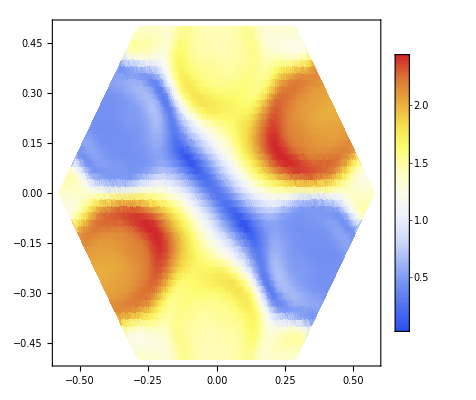
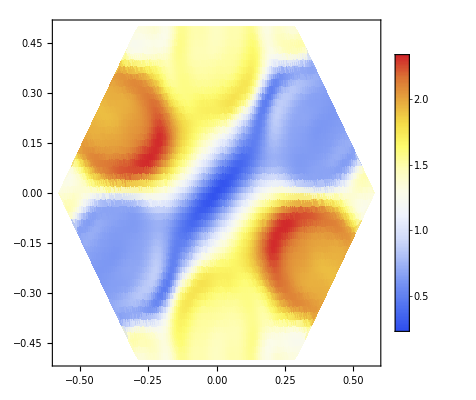

```mathematica
{ListDensityPlot[LSqH1zk1, ColorFunction->"TemperatureMap",PlotRange->All,PlotLegends->Automatic],
ListDensityPlot[LSqH2zk1, ColorFunction->"TemperatureMap",PlotRange->All,PlotLegends->Automatic]}
```

Evaluating D Fields

```mathematica
LSqD1k1=ParallelTable[{r⟦1⟧,r⟦2⟧,Abs[D1xk1[r⟦1⟧,r⟦2⟧]]^2+Abs[D1yk1[r⟦1⟧,r⟦2⟧]]^2},{r, RHex}];
LSqD2k1=ParallelTable[{r⟦1⟧,r⟦2⟧,Abs[D2xk1[r⟦1⟧,r⟦2⟧]]^2+Abs[D2yk1[r⟦1⟧,r⟦2⟧]]^2},{r, RHex}];
```

```mathematica
Export["SqD1k1.dat",LSqD1k1,"Table"];
Export["SqD2k1.dat",LSqD2k1,"Table"];
```

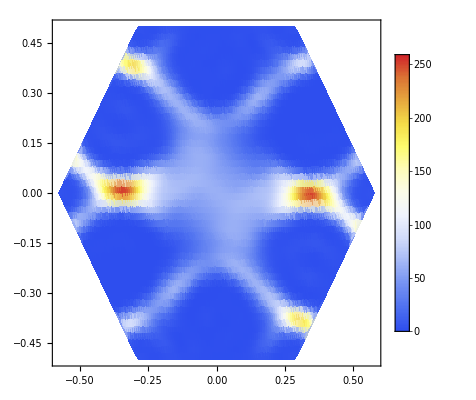
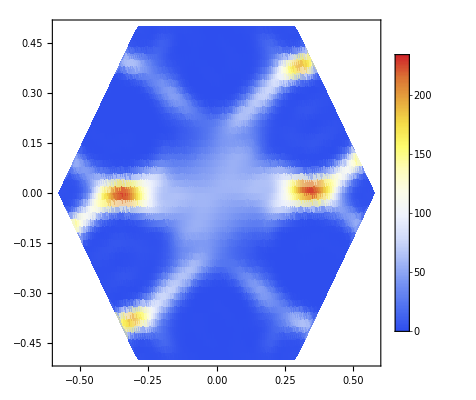

```mathematica
{ListDensityPlot[LSqD1k1, ColorFunction->"TemperatureMap",PlotRange->All,PlotLegends->Automatic],ListDensityPlot[LSqD2k1, ColorFunction->"TemperatureMap",PlotRange->All,PlotLegends->Automatic]}
```

Evaluating E Field

```mathematica
LSqE1k1=ParallelTable[{r⟦1⟧,r⟦2⟧,Sqrt[Abs[E1xk1[r⟦1⟧,r⟦2⟧]]^2+Abs[E1yk1[r⟦1⟧,r⟦2⟧]]^2]},{r, RHex}];
LSqE2k1=ParallelTable[{r⟦1⟧,r⟦2⟧,Sqrt[Abs[E2xk1[r⟦1⟧,r⟦2⟧]]^2+Abs[E2yk1[r⟦1⟧,r⟦2⟧]]^2]},{r, RHex}];
```

```mathematica
Export["SqE1k1.dat",LSqE1k1,"Table"];
Export["SqE2k1.dat",LSqE2k1,"Table"];
```

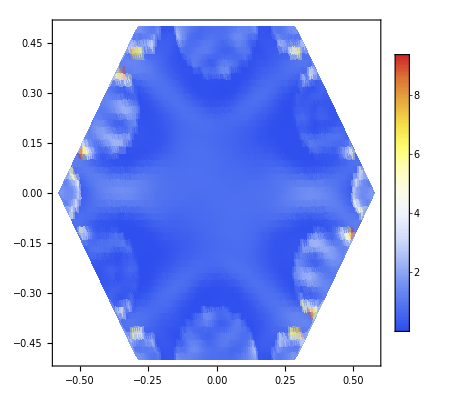
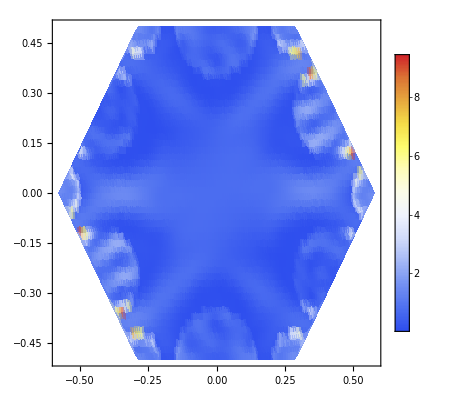

```mathematica
{ListDensityPlot[LSqE1k1, ColorFunction->"TemperatureMap",PlotRange->All,PlotLegends->Automatic],ListDensityPlot[LSqE2k1, ColorFunction->"TemperatureMap",PlotRange->All,PlotLegends->Automatic]}
```

```mathematica
Clear[LSqH1zk1,LSqH2zk1]
Clear[LSqD1k1,LSqD2k1]
Clear[LSqE1k1,LSqE2k1]
```

k_1’ - Fields for the two first bands in k close to the Dirac cone at K’ ----------------------------------------------------------------------------------

```mathematica
Δk[k_,ϕ_]:=k{Cos[ϕ],Sin[ϕ]};
Nq=0.03 Norm[{kx,ky}];ϕq=0;
kp1={kx,-ky}+Δk[Nq,ϕq];
Export["kp1-gmax_"<>ToString[gx]<>"-Ng_"<>ToString[Ng]<>".dat",{kp1},"Table"];
```

k_1 -----------------------------------------------------------------------------------

```mathematica
Ti=AbsoluteTime[];
WV[kp1,2,1];
Tf=AbsoluteTime[]-Ti
Export["MatrixGME-kp1-gmax_"<>ToString[gx]<>"-Ng_"<>ToString[Ng]<>".dat",MM,"Table"];
Dxxkp1=Dxx/.z-> 0;
Dyykp1=Dxx/.z-> 0;
Hzzkp1=Hzz/.z-> 0;
Hzkp1[xp_,yp_]=(Hzzkp1/.x-> xp /.y-> yp);
Dxkp1[xp_,yp_]=(Dxxkp1/.x-> xp /.y-> yp);
Dykp1[xp_,yp_]=(Dyykp1/.x-> xp /.y-> yp);
Exkp1[xp_,yp_]=(Dxxkp1/.x-> xp /.y-> yp)/Eps[xp,yp];
Eykp1[xp_,yp_]=(Dyykp1/.x-> xp /.y-> yp)/Eps[xp,yp];
```

105.571255

{0.446625,0.434835}

```mathematica
H1zkp1[x_,y_]=Hzkp1[x,y]⟦1⟧;H2zkp1[x_,y_]=Hzkp1[x,y]⟦2⟧;

D1xkp1[x_,y_]=Dxkp1[x,y]⟦1⟧;D2xkp1[x_,y_]=Dxkp1[x,y]⟦2⟧;
D1ykp1[x_,y_]=Dykp1[x,y]⟦1⟧;D2ykp1[x_,y_]=Dykp1[x,y]⟦2⟧;

E1xkp1[x_,y_]=Exkp1[x,y]⟦1⟧;E2xkp1[x_,y_]=Exkp1[x,y]⟦2⟧;
E1ykp1[x_,y_]=Eykp1[x,y]⟦1⟧;E2ykp1[x_,y_]=Eykp1[x,y]⟦2⟧;
```

Evaluate H Field

```mathematica
(********************Band 1********************)
LSqH1zkp1= ParallelTable[{r⟦1⟧,r⟦2⟧,Sqrt[Abs[H1zkp1[r⟦1⟧,r⟦2⟧]]^2]},{r, RHex}];
(********************Band 2********************)
LSqH2zkp1= ParallelTable[{r⟦1⟧,r⟦2⟧,Sqrt[Abs[H2zkp1[r⟦1⟧,r⟦2⟧]]^2]},{r, RHex}];
```

```mathematica
Export["SqH1zkp1.dat",LSqH1zkp1,"Table"];
Export["SqH2zkp1.dat",LSqH2zkp1,"Table"];
```

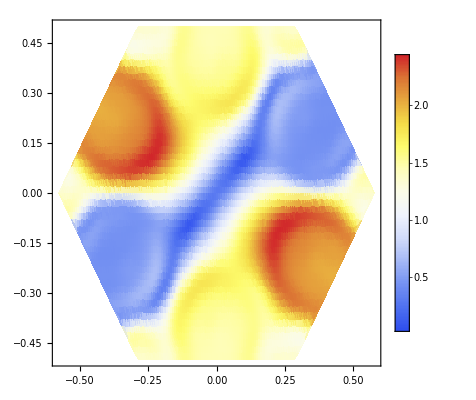
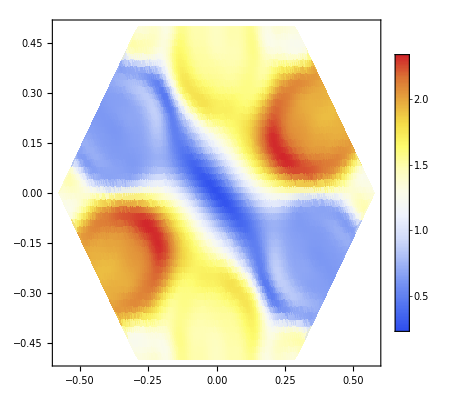

```mathematica
{ListDensityPlot[LSqH1zkp1, ColorFunction->"TemperatureMap",PlotRange->All,PlotLegends->Automatic],ListDensityPlot[LSqH2zkp1, ColorFunction->"TemperatureMap",PlotRange->All,PlotLegends->Automatic]}
```

Evaluate D Field

```mathematica
LSqD1kp1=ParallelTable[{r⟦1⟧,r⟦2⟧,Abs[D1xkp1[r⟦1⟧,r⟦2⟧]]^2+Abs[D1ykp1[r⟦1⟧,r⟦2⟧]]^2},{r, RHex}];
LSqD2kp1=ParallelTable[{r⟦1⟧,r⟦2⟧,Abs[D2xkp1[r⟦1⟧,r⟦2⟧]]^2+Abs[D2ykp1[r⟦1⟧,r⟦2⟧]]^2},{r, RHex}];
```

```mathematica
Export["SqD1kp1.dat",LSqD1kp1,"Table"];
Export["SqD2kp1.dat",LSqD2kp1,"Table"];
```

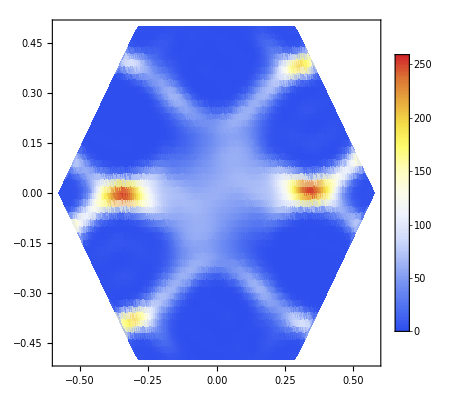
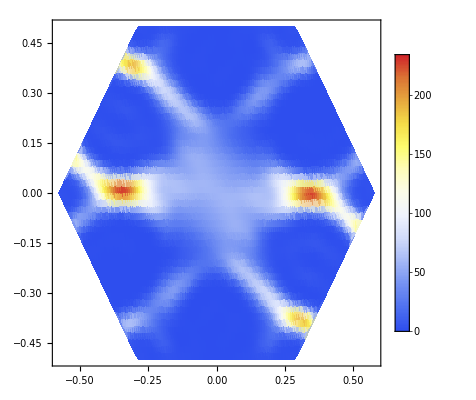

```mathematica
{ListDensityPlot[LSqD1kp1, ColorFunction->"TemperatureMap",PlotRange->All,PlotLegends->Automatic],ListDensityPlot[LSqD2kp1, ColorFunction->"TemperatureMap",PlotRange->All,PlotLegends->Automatic]}
```

Evaluate E Field

```mathematica
LSqE1kp1=ParallelTable[{r⟦1⟧,r⟦2⟧,Sqrt[Abs[E1xkp1[r⟦1⟧,r⟦2⟧]]^2+Abs[E1ykp1[r⟦1⟧,r⟦2⟧]]^2]},{r, RHex}];
LSqE2kp1=ParallelTable[{r⟦1⟧,r⟦2⟧,Sqrt[Abs[E2xkp1[r⟦1⟧,r⟦2⟧]]^2+Abs[E2ykp1[r⟦1⟧,r⟦2⟧]]^2]},{r, RHex}];
```

```mathematica
Export["SqE1kp1.dat",LSqE1kp1,"Table"];
Export["SqE2kp1.dat",LSqE2kp1,"Table"];
```

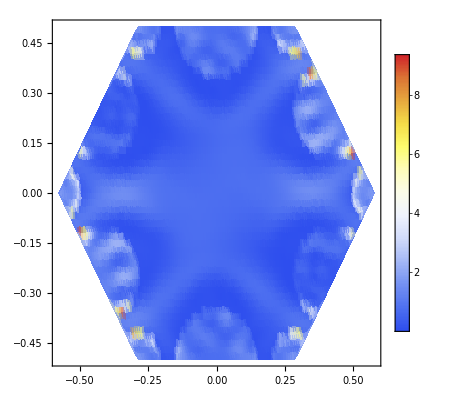
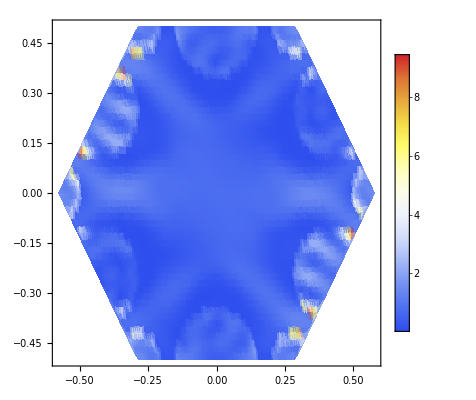

```mathematica
{ListDensityPlot[LSqE1kp1, ColorFunction->"TemperatureMap",PlotRange->All,PlotLegends->Automatic],ListDensityPlot[LSqE2kp1, ColorFunction->"TemperatureMap",PlotRange->All,PlotLegends->Automatic]}
```

```mathematica
Clear[LSqH1zk1,LSqH2zk1]
Clear[LSqD1k1,LSqD2k1]
Clear[LSqE1k1,LSqE2k1]
```

### Recording matrix for the GME’s Eigenproblem

#### K

```mathematica
K0={kx,ky}; (*K point*)
TGMEi=AbsoluteTime[];
WV[K0,2,1];
TGMEf=AbsoluteTime[]-TGMEi
```

108.068596

```mathematica
Export["MatrixGME-kx_"<>ToString[K0⟦1⟧]<>"-ky_"<>ToString[K0⟦2⟧]<>"-gmax_"<>ToString[gx]<>"-Ng_"<>ToString[Ng]<>".dat",MM,"Table"];
MM=Import["MatrixGME-kx_"<>ToString[K0⟦1⟧]<>"-ky_"<>ToString[K0⟦2⟧]<>"-gmax_"<>ToString[gx]<>"-Ng_"<>ToString[Ng]<>".dat","Table"];
```

#### K’

```mathematica
Kp0={kx,-ky}; (*K' point*)
TGMEi=AbsoluteTime[];
WV[Kp0,2,1];
TGMEf=AbsoluteTime[]-TGMEi
```

108.452028

```mathematica
Export["MatrixGME-kx_"<>ToString[Kp0⟦1⟧]<>"-ky_"<>ToString[Kp0⟦2⟧]<>"-gmax_"<>ToString[gx]<>"-Ng_"<>ToString[Ng]<>".dat",MM,"Table"];
MM=Import["MatrixGME-kx_"<>ToString[Kp0⟦1⟧]<>"-ky_"<>ToString[Kp0⟦2⟧]<>"-gmax_"<>ToString[gx]<>"-Ng_"<>ToString[Ng]<>".dat","Table"];
Dimensions[MM]
```

{888,888}

### Band structure

Here, the notebook evaluates the eigenfrequencies at several k-point. First, we scanning the edge of the Irreducible Brillouin; and second, we scanning square areas around the Dirac cones at K and K’

#### k’s mesh in IBZ edge

```mathematica
nk=20;
(*  Gamma: (kx=0,ky=0) ; M: (kx=2π/√3,ky=0) ; K: (kx=2π/√3,ky=2π/3) *)
K1={0.0000001,0.0};K2={2Pi/Sqrt[3],0};K3={2Pi/Sqrt[3],2Pi/3};
K12=Table[N[Join[{Norm[K2-K1]i/(nk+1)},(K2-K1)i/(nk+1)+K1]],{i,0,nk+1}];
K23=Table[N[Join[{Norm[K2-K1]+N[Norm[K3-K2]]i/(nk+1)},(K3-K2)i/(nk+1)+K2]],{i,nk+1}];
K31=Table[N[Join[{Norm[K2-K1]+N[Norm[K3-K2]]+N[Norm[K1-K3]]i/(nk+1)},(K1-K3)i/(nk+1)+K3]],{i,nk+1}];
ks=Join[K12,K23,K31];
Print["Total evaluated k-points in the IBZ edge: ", Length[ks]]
```

Total evaluated k-points in the IBZ edge: 64

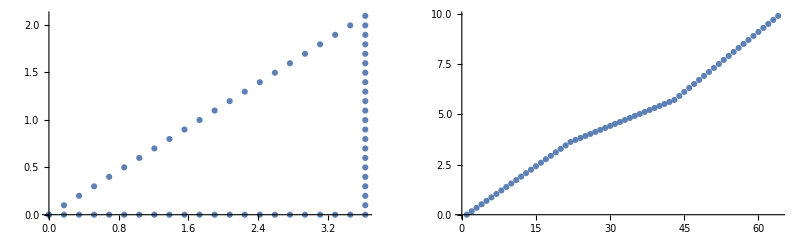

```mathematica
GraphicsGrid[{{ListPlot[ks⟦All,2;;3⟧],ListPlot[ks⟦All,1⟧]}}] (*Graphics of the IBZ and the lenght parameterization*)
```

#### Evaluating WV in IBZ

```mathematica
nb=4;
SetSharedVariable[Freqs];
Freqs=ConstantArray[0,{Length[ks]*nb}];
```

```mathematica
T1=AbsoluteTime[];
ParallelDo[t0=AbsoluteTime[];
Eigenk=WV[{ks⟦ik,2⟧,ks⟦ik,3⟧},nb,1];
Freqs⟦nb(ik-1)+1;;nb(ik)⟧=Table[Join[ks⟦ik⟧,{i},{Eigenk⟦2,i⟧}],{i,nb}];
Print[ik,"/",Length[ks],": ", AbsoluteTime[]-t0],{ik,2,Length[ks]-1}];T=AbsoluteTime[]-T1
```

2/64: 153.659269

26/64: 154.654607

10/64: 155.713774

14/64: 155.965102

30/64: 156.727067

6/64: 156.88265

18/64: 156.963435

22/64: 157.041226

3/64: 165.227493

27/64: 167.004284

23/64: 166.432359

11/64: 167.96526

15/64: 167.981217

31/64: 167.67603

19/64: 168.860394

7/64: 171.231053

4/64: 168.139085

28/64: 166.944551

24/64: 165.271477

20/64: 164.902529

16/64: 168.170329

12/64: 168.654059

32/64: 168.70689

8/64: 165.295484

29/64: 156.433843

25/64: 159.685711

5/64: 161.780915

21/64: 158.466402

17/64: 158.994949

13/64: 160.484529

9/64: 160.632664

33/64: 161.287919

34/64: 153.986423

42/64: 152.743745

38/64: 154.560882

46/64: 156.049003

50/64: 155.279978

61/64: 153.482278

54/64: 157.198874

58/64: 157.497604

35/64: 152.163151

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

43/64: 150.780859

39/64: 151.581708

47/64: 152.740549

51/64: 153.652658

62/64: 153.812234

55/64: 152.760047

59/64: 154.093471

44/64: 155.266787

36/64: 157.619

40/64: 156.621295

52/64: 154.219254

48/64: 157.902454

56/64: 154.896439

63/64: 156.598917

60/64: 154.94245

45/64: 141.774568

41/64: 138.792452

37/64: 141.833482

53/64: 139.916548

49/64: 141.128927

57/64: 140.382716

1317.634081

```mathematica
Export["FreqsIBZ-gmax_"<>ToString[gx]<>"-Ng_"<>ToString[Ng]<>".dat",Flatten[Freqs⟦nb+1;;-(nb+1)⟧,1],"Table"]
```

FreqsIBZ-gmax_9-Ng_3.dat

```mathematica
Freq=Partition[Freqs⟦nb+1;;-(nb+1),{1,5}⟧,nb];
Dimensions[Freq]
LightCone=Join[{{0,0}},Table[{f⟦1⟧,Norm[f⟦{2,3}⟧]/(2π)},{f,Freqs⟦nb+1;;-(nb+1)⟧}],{{ks⟦-1,1⟧,0}}];
```

{62,4,2}

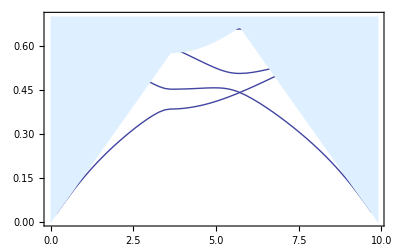

```mathematica
BandGrap=ListPlot[Transpose[Freq],Joined->True,PlotStyle->{{RGBColor[0.26,0.27,0.63],Thick}},Frame->{{True,None},{True,None}},LabelStyle->Directive[Bold,Large],PlotRange->{{0,Max[Freq⟦All,All,1⟧]+(Freq⟦2,1,1⟧-Freq⟦1,1,1⟧)},{0,0.7}}];
LConeGrap=ListPlot[LightCone,Joined->True,PlotStyle->{{LightBlue,Thick}},LabelStyle->Directive[Bold,Large],Filling->{1-> {0.7,LightBlue}},FillingStyle->LightBlue];
Show[BandGrap,LConeGrap]
```

#### k’s mesh at Dirac Cone in K

```mathematica
(**************************************************)
Δp=Δpx=Δpy=0.014;
k=4 Pi/(3 a);
kxi=Sqrt[3]/2 k;
kyi=1/2 k;
Δk=0.02* 2 Pi/a;
kk=Round[0.02* 2 Pi/a/Δp];
ks1=Table[{kxi+i*Δpx,kyi+j*Δpy,Δpx*Δpy},{i,-kk,kk},{j,-kk,kk}];
ks2=Table[{kxi+i*Δpx,-kyi+j*Δpy,Δpx*Δpy},{i,-kk,kk},{j,-kk,kk}];
ks0=Join[Flatten[ks1,1],Flatten[ks2,1]];
lk=Flatten[ks1,1];
Print["Δpx: ",Δpx,", Δpy: ",Δpy, ", Number of Points in k: ",Length[lk]]
Print["Approx Time: ", N[Length[lk]/8*3],"min"]
```

Δpx: 0.014, Δpy: 0.014, Number of Points in k: 361

Approx Time: 135.375min

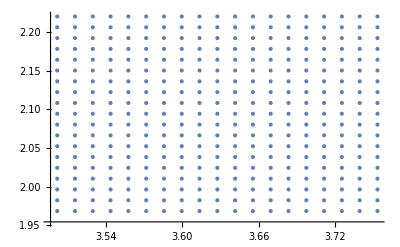

```mathematica
ListPlot[{lk⟦All,1;;2⟧}] (*Mesh around K point*)
```

#### Dirac Cone at K

```mathematica
nb=2;
SetSharedVariable[FreqsSurf];
FreqsSurf=ConstantArray[0,{Length[lk]*nb}];
```

```mathematica
T1=AbsoluteTime[];
ParallelDo[t0=AbsoluteTime[];
Eigenk=WV[{lk⟦ik,1⟧,lk⟦ik,2⟧},nb,1];
FreqsSurf⟦nb(ik-1)+1;;nb(ik)⟧=Table[Join[lk⟦ik⟧,{i},{Eigenk⟦2,i⟧}],{i,nb}];
Print[ik,"/",Length[lk],": ", AbsoluteTime[]-t0],{ik,Length[lk]}];T=AbsoluteTime[]-T1
```

271/361: 159.091363

217/361: 158.38584

195/361: 157.997351

206/361: 159.201348

239/361: 160.096381

228/361: 160.079312

250/361: 158.263589

261/361: 159.693337

272/361: 155.975306

218/361: 155.539842

207/361: 154.255348

196/361: 157.845344

229/361: 155.884468

240/361: 157.566729

251/361: 155.905911

262/361: 156.99365

273/361: 156.326331

285/361: 154.619394

274/361: 158.953387

296/361: 160.298749

307/361: 158.457394

318/361: 158.344272

329/361: 156.884548

340/361: 155.447394

351/361: 156.082274

286/361: 158.463314

275/361: 157.16533

308/361: 155.876295

297/361: 156.982279

319/361: 156.376408

330/361: 155.386448

341/361: 158.693206

352/361: 158.627331

276/361: 155.83012

287/361: 158.152466

309/361: 158.167527

298/361: 158.216548

320/361: 157.455401

331/361: 156.221277

342/361: 158.070492

353/361: 154.939558

277/361: 154.804679

288/361: 157.76037

299/361: 155.543229

321/361: 157.504323

310/361: 158.735495

332/361: 157.167381

343/361: 155.775211

354/361: 155.133244

278/361: 153.889252

289/361: 155.586611

300/361: 154.51901

322/361: 156.541804

333/361: 155.016289

311/361: 157.662147

344/361: 157.122074

355/361: 154.822359

279/361: 154.345334

290/361: 155.49111

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

301/361: 157.905819

323/361: 155.213552

334/361: 155.683496

312/361: 157.268764

345/361: 158.991764

356/361: 154.835411

280/361: 154.987922

291/361: 156.379314

302/361: 155.291282

324/361: 156.781741

335/361: 155.018276

313/361: 155.438034

346/361: 154.354369

357/361: 154.040967

281/361: 155.475838

292/361: 155.381452

303/361: 156.150367

325/361: 155.609755

336/361: 155.907582

314/361: 155.223248

347/361: 156.870384

358/361: 154.963042

282/361: 155.384568

293/361: 155.246292

304/361: 156.223729

326/361: 155.312606

337/361: 158.40047

315/361: 158.363347

348/361: 156.362757

359/361: 152.251375

283/361: 155.857391

294/361: 153.861216

305/361: 155.466576

327/361: 156.373547

338/361: 154.888096

316/361: 155.456577

349/361: 154.950426

360/361: 155.45296

284/361: 155.015407

295/361: 155.627232

306/361: 155.538444

328/361: 155.253632

339/361: 155.394752

317/361: 155.087684

350/361: 140.904631

361/361: 115.559974

7132.5456606

```mathematica
Export["FreqsSurfK-gmax_"<>ToString[gx]<>"-Ng_"<>ToString[Ng]<>".dat",Flatten[FreqsSurf,1],"Table"]
```

FreqsSurfK-gmax_9-Ng_3.dat

```mathematica
ListPlot3D[{FreqsSurf⟦1;;-1;;2,{1,2,5}⟧,FreqsSurf⟦2;;-1;;2,{1,2,5}⟧},PlotRange->All,PlotStyle->Directive[Blue,Specularity[White,0.6]],Mesh-> True,AspectRatio->1]
```

-Graphics3D-

```mathematica
Export["frec1.dat",FreqsSurf⟦1;;-1;;2,{1,2,5}⟧,"Table"]
Export["frec2.dat",FreqsSurf⟦2;;-1;;2,{1,2,5}⟧,"Table"]
```

frec1.dat

frec2.dat